```mathematica
SetDirectory[NotebookDirectory[]];
options3={Frame->{True,True,False,False},FrameStyle->Black,BaseStyle->{FontSize->20},LabelStyle->Black};
fNumericMean[aX_,α_,β_,y0_]:=Module[{y,x,f=NDSolveValue[{y'[x]==α y[x](1-β y[x]),y[0]==y0},y,{x,0,100}]},f[aX]]
fMean[x_,α_,β_,y0_]:=(ⅇ^(x α) y0)/(1-y0 β+ⅇ^(x α) y0 β)
fYGenerate[x_,α_,β_,y0_,σ_]:=RandomVariate[NormalDistribution[fMean[x,α,β,y0],σ],{1}][[1]]
fGenerateY[]:=Block[{lX =Table[x,{x,{1,1+2.7,1+2 2.7, 9.5}}],lY},lX=lX+RandomVariate[NormalDistribution[0,0.1],Length@lX];Thread[{lX,fYGenerate[#,0.5,0.05,5,3]&/@lX}]]
```

## Snapshots vs time series

```mathematica
data=Table[fGenerateY[],{i,1,10,1}];
```

```mathematica
Needs["PolygonPlotMarkers`"]

allShapes=PolygonMarker[All];
Tooltip[Graphics[{FaceForm[Hue@Random[]],EdgeForm[{Black,Thickness[0.003],JoinForm["Miter"]}],PolygonMarker[#,1]},ImageSize->30,PlotRange->1.5,PlotRangePadding->0,ImagePadding->0],#]&/@allShapes;
allShapes = RandomSample[allShapes[[1;;30]]];
graphs=Graphics[{FaceForm[Blue],PolygonMarker[ToString@#,Scaled[0.04]]},AlignmentPoint->{0,0}]&/@allShapes[[3;;13]];
```

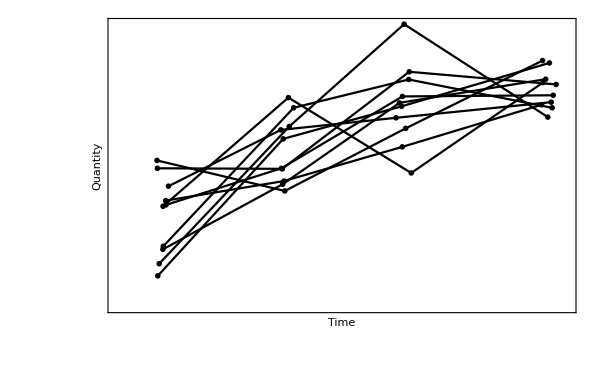
-Graphics-A. Time series

```mathematica
ga1=Labeled[ListLinePlot[data,PlotStyle->Black,PlotRange->{{0,10},Full},Joined->True,PlotMarkers ->graphs,ImageSize->600,FrameTicks->None,FrameStyle->Directive[Black,20,Thick],Frame->{True,True,False,False},FrameLabel->{"Time","Quantity"},ImagePadding->{{30,None},{30,None}}],"A. Time series", {{Top,Left}},LabelStyle->{Black,FontSize->20}]
```

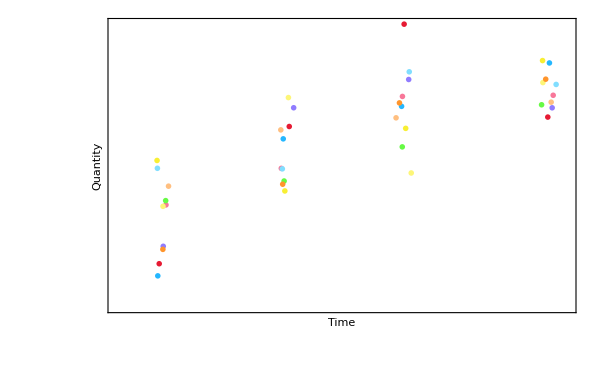
-Graphics-B. Snapshots

```mathematica
ga2=Labeled[ListPlot[data,PlotStyle->"BrightBands",PlotRange->{{0,10},Full},PlotMarkers ->Graphics[{FaceForm[Blue],PolygonMarker[ToString@"Disk",Scaled[0.04]]},AlignmentPoint->{0,0}],ImageSize->600,FrameTicks->None,FrameStyle->Directive[Black,20,Thick],Frame->{True,True,False,False},FrameLabel->{"Time","Quantity"},ImagePadding->{{30,None},{30,None}}],"B. Snapshots", {{Top,Left}},LabelStyle->{Black,FontSize->20}]
```

```mathematica
gFinal=GraphicsRow[{ga1,ga2},ImageSize->1300,Spacings->0]
```

-Graphics-

```mathematica
Export["../figures/time_series_v_snapshots.pdf",gFinal]
```

../figures/time_series_v_snapshots.pdf

## Many snapshots

```mathematica
fGenerateY1[sigma__]:=Block[{lX =Table[x,{x,{1,1+2.7,1+2 2.7, 9.5}}],lY},lX=lX+RandomVariate[NormalDistribution[0,0.1],Length@lX];Table[{lX[[i]],fYGenerate[lX[[i]],0.5,0.05,5,sigma[[i]]]},{i,1,Length@lX,1}]]
```

```mathematica
data=Table[fGenerateY1[{1,2,3,1.5}],{i,1,50,1}];
```

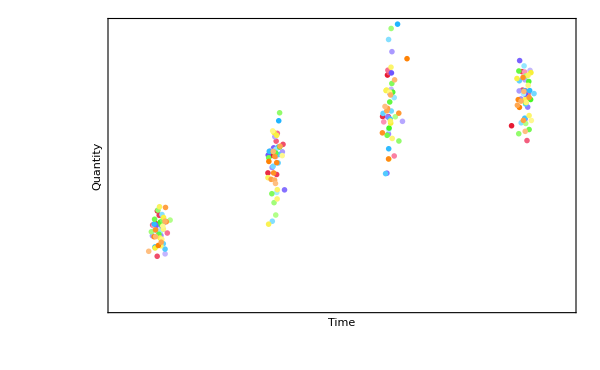

```mathematica
gsingle=ListPlot[data,PlotStyle->"BrightBands",PlotRange->{{0,10.5},Full},PlotMarkers ->Graphics[{FaceForm[Blue],PolygonMarker[ToString@"Disk",Scaled[0.04]]},AlignmentPoint->{0,0}],ImageSize->600,FrameTicks->None,FrameStyle->Directive[Black,20,Thick],Frame->{True,True,False,False},FrameLabel->{"Time","Quantity"},ImagePadding->{{30,None},{30,None}}]
```

```mathematica
aPlot1=Plot[PDF[NormalDistribution[0,0.002],x],{x,-0.015,0.015},Axes->None,PlotStyle->Directive[Black,Dashed],Filling->Bottom,FillingStyle->Opacity[0.7,Gray],AspectRatio->1/3,PlotRange->{Automatic,{0,221}}];
aPlot2=Plot[PDF[NormalDistribution[0,0.003],x],{x,-0.015,0.015},Axes->None,PlotStyle->Directive[Black,Dashed],Filling->Bottom,FillingStyle->Opacity[0.7,Gray],AspectRatio->1/3,PlotRange->{Automatic,{0,221}}];
aPlot3=Plot[PDF[NormalDistribution[0,0.005],x],{x,-0.015,0.015},Axes->None,PlotStyle->Directive[Black,Dashed],Filling->Bottom,FillingStyle->Opacity[0.7,Gray],AspectRatio->1/3,PlotRange->{Automatic,{0,221}}];
aPlot4=Plot[PDF[NormalDistribution[0,0.0025],x],{x,-0.015,0.015},Axes->None,PlotStyle->Directive[Black,Dashed],Filling->Bottom,FillingStyle->Opacity[0.7,Gray],AspectRatio->1/3,PlotRange->{Automatic,{0,221}}];
```

```mathematica
Show[gsingle,Graphics[Inset[Rotate[aPlot1,3Pi /2],{1.7,fMean[1,0.5,0.05,5]}]],Graphics[Inset[Rotate[aPlot2,3Pi /2],{4.5,fMean[1+2.7,0.5,0.05,5]}]],Graphics[Inset[Rotate[aPlot3,3Pi /2],{4.5+2.7,fMean[1+2.7 2,0.5,0.05,5]}]],Graphics[Inset[Rotate[aPlot3,3Pi /2],{10.2,fMean[9.5,0.5,0.05,5]}]]]
```

-Graphics-

```mathematica
aDist=MultinormalDistribution[{0.65,2},{{0.05,-0.03},{-0.03,0.05}}];
bDist=MultinormalDistribution[{2,0.5},{{0.2,0.0},{0.00,0.01}}];
```

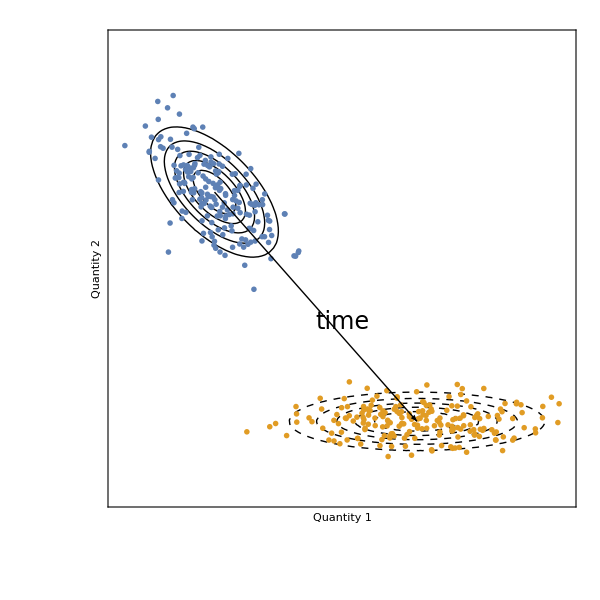

```mathematica
Show[ContourPlot[PDF[aDist,{x,y}],{x,0,3},{y,0,3},PlotRange->{{0,3},{0,3},Full},Contours->5,ImageSize->600,FrameTicks->None,FrameStyle->Directive[Black,20,Thick],Frame->{True,True,False,False},FrameLabel->{"Quantity 1","Quantity 2"},ImagePadding->{{30,None},{30,None}},ContourShading->None],ContourPlot[PDF[bDist,{x,y}],{x,0,3},{y,0,3},PlotRange->{{0,3},{0,3},Full},Contours->5,ImageSize->600,FrameTicks->None,FrameStyle->Directive[Black,20,Thick],Frame->{True,True,False,False},FrameLabel->{"Quantity 1","Quantity 2"},ImagePadding->{{30,None},{30,None}},ContourShading->None,ContourStyle->Dashed],ListPlot[{RandomVariate[aDist,{200}],RandomVariate[bDist,{200}]},PlotRange->{{0,3},{0,3}},PlotMarkers ->{Graphics[{FaceForm[Opacity[0.5,Blue]],PolygonMarker[ToString@"Disk",Scaled[0.04]]},AlignmentPoint->{0,0}],Graphics[{FaceForm[Opacity[0.7,Orange]],PolygonMarker[ToString@"Disk",Scaled[0.04]]},AlignmentPoint->{0,0}]},ImageSize->600,FrameTicks->None,FrameStyle->Directive[Black,20,Thick],Frame->{True,True,False,False},FrameLabel->{"Quantity 1","Quantity 2"},ImagePadding->{{30,None},{30,None}}],Graphics[{Arrow[{{0.65,2},{2,0.5}}]}],Graphics[Rotate[Text[Style["time",FontSize->24],{1.5,1.15}],-0.27 Pi]]]
```